# Predict the Scale of Satellite Images

Some explanation

Mehmet Sahin, Jun. 26,  2018

Some explanation

```mathematica
Quit
```

## Collect Satellite Images

In this section, we will get the data using GeoImage.

Some explanation

```mathematica
ClearAll["Global`*"]
```

Create a function to get countries’ geo positions randomly:

```mathematica
ClearAll[geoPositionOfCountry]
geoPositionOfCountry[entities_,numberOfPosition_Integer,folderName_String] :=
	Module[
		{countries, mesh},
		countries = entities;
		mesh = DiscretizeGraphics@EntityValue[countries,"Polygon"];
		SeedRandom[Hash@{folderName,countries,RandomReal[{1,5}]}];
		Reverse[RandomPoint[mesh,numberOfPosition],{2}]
	]
```

Let’s plot them and see how those random positions act on a Graphic

```mathematica
(*trainingDataOfCountry = geoPositionOfCountry[{Entity["Country","UnitedStates"]},500,"training"];
validationDataOfCountry = geoPositionOfCountry[{Entity["Country","UnitedStates"]},100,"validation"];
testingDataOfCountry = geoPositionOfCountry[{Entity["Country","UnitedStates"]},25,"testing"];*)

trainingDataOfCities = geoPositionOfCountry[{},100,"training"];
trainingDataOfCitiesA = geoPositionOfCountry[{Entity["City",{"Austin","Texas","UnitedStates"}]},100,"training"];
(*validationDataOfCities = geoPositionOfCountry[{},100,"validation"];
testingDataOfCities = geoPositionOfCountry[{},50,"testing"];*)

(*GeoListPlot@GeoPosition@trainingDataOfCountry*)
GeoListPlot@GeoPosition@trainingDataOfCitiesA
```

-Graphics-

Old normaliser function:

```mathematica
(*b = geoPositionOfCountry[{},50,"testing"];
ClearAll[getZoomLevel, getGeoRange]
SetAttributes[getGeoRange, Listable]
(*Rondom point distrubition*)
(*getZoomLevel[point_List,max_] := 
	With[
		{cutoff = 0.05},
		SeedRandom[Hash[point]]; 
		Clip[RandomVariate[HalfNormalDistribution[ If[max≤10,2,5]]],{0,1 - cutoff}] + cutoff
	];*)
getZoomLevel[] := 
	With[
	{random =RandomReal[]},
	If[random<0.1,0.1,random]  (*0.2*)  
	];

randomPoints = getZoomLevel[]& /@ b; 
ListPlot[randomPoints]
Histogram[randomPoints,PlotRange->All]
randomPoints
Count[randomPoints,y_/;y<0.5]

(*getGeoRange[zoom_,max_] := zoom * max; *)
getGeoRange[zoom_,max_] := Round[zoom * max,0.1]; (*no round !*)
getGeoRange[#,10]& /@  randomPoints*)
```

4.15656

New normaliser function for geo range:

{0.,0.0968016,0.146724,0.187135,0.222392,0.254252,0.283644,0.311129,0.337083,0.361766,0.385374,0.408054,0.429923,0.451075,0.471584,0.491515,0.510922,0.529848,0.548335,0.566415,0.584118,0.60147,0.618495,0.635213,0.651642,0.6678,0.683701,0.69936,0.714788,0.729997,0.744998,0.7598,0.774412,0.788843,0.8031,0.81719,0.83112,0.844896,0.858524,0.872009,0.885357,0.898572,0.911658,0.92462,0.937463,0.950189,0.962802,0.975306,0.987705,1.}

{0.2,0.567846,0.75755,0.911113,1.04509,1.16616,1.27785,1.38229,1.48091,1.57471,1.66442,1.75061,1.83371,1.91408,1.99202,2.06776,2.1415,2.21342,2.28367,2.35238,2.41965,2.48559,2.55028,2.61381,2.67624,2.73764,2.79806,2.85757,2.91619,2.97399,3.03099,3.08724,3.14277,3.1976,3.25178,3.30532,3.35826,3.41061,3.46239,3.51364,3.56436,3.61457,3.6643,3.71356,3.76236,3.81072,3.85865,3.90616,3.95328,4.}

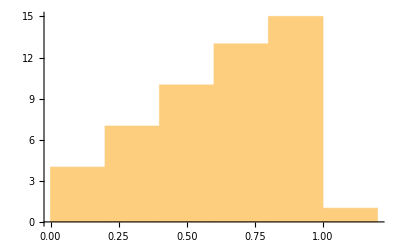

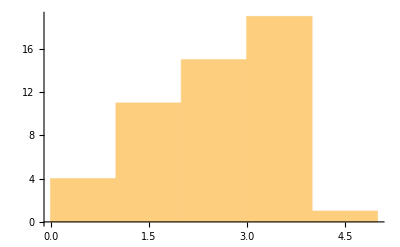

```mathematica
ClearAll[pointRange, rescale, getZoomLevel,getGeoRange,zoomLevel,geoRange,revertRescale,function]
SetAttributes[{rescale, revertRescale}, Listable]

$minscale = 0.2;
$maxscale = 4;

rescale[x_, min_: $minscale, max_: $maxscale] := 
 (x - min) / (max - min)
revertRescale[x_, min_: $minscale, max_: $maxscale] := 
 min + x * (max - min)
pointRange[zmin_:$minscale, zmax_:$maxscale, length_: 10]  := 
 Table[
  rescale[x], 
  {x, zmin, zmax, (zmax - zmin) / (length - 1)}
  ]

function = Function[#^(0.6)];
(*rescale[x_, min_, max_] := 
 (x - min) / (max - min)
revertRescale[x_, min_:0, max_:1] := 
 min + x * (max - min)
pointRange[zmin_, zmax_, length_]  := 
 Table[
  rescale[x,zmin,zmax], 
  {x, zmin, zmax, (zmax - zmin) / (length - 1)}
  ]*)
  
  
getZoomLevel[zmin_, zmax_, length_] := 
	With[
		{range = pointRange[zmin,zmax,length]},
		Map[function, rescale[range, Min[range], Max[range]]]
	];
getGeoRange[zoomLevel_] := 
	revertRescale @ revertRescale[zoomLevel, Min[zoomLevel], Max[zoomLevel]];
	

(*range = pointRange[0.2,20,5] (* LINEAR we don't use them *)
rescaled = Map[function, rescale[range, Min[range], Max[range]]] (* ML VALUES *)
reverted = revertRescale [ revertRescale[rescaled],0.2,20] (* what you store in values *)
MLValues = rescale[reverted, Min[reverted], Max[reverted]] (* ML VALUES *)
MLResults = revertRescale[MLValues, Min[reverted], Max[reverted]] (* Actual results *)*)

zoomLevel = getZoomLevel[0.2,4,50]
geoRange = getGeoRange[zoomLevel]

(*range = pointRange[0.2,10,5] (* LINEAR we don't use them *)
rescaled = Map[function, rescale[range, Min[range], Max[range]]] (* ML VALUES *)
reverted = revertRescale @ revertRescale[rescaled, Min[range], Max[range]] (* what you store in values *)
MLValues = rescale[reverted, Min[reverted], Max[reverted]] (* ML VALUES *)
MLResults = revertRescale[MLValues, Min[reverted], Max[reverted]] (* Actual results *)
*)
(*rescaled // ListPlot
reverted // Histogram*)
Histogram[zoomLevel,PlotRange->All]
Histogram[geoRange,PlotRange->All]
```

```mathematica
ClearAll[zoomLevel,geoRange]
zoomLevel = getZoomLevel[0.2,10,Length@trainingDataOfCities]; (*/@ trainingDataOfCities;*)
geoRange = getGeoRange[zoomLevel];(*Map[getGeoRange,zoomLevel];*)
```

Check the distribution of points and zoom level:

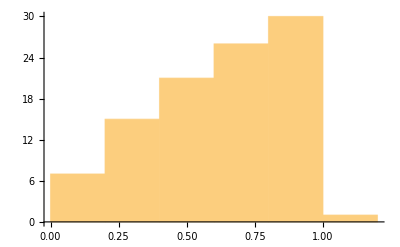

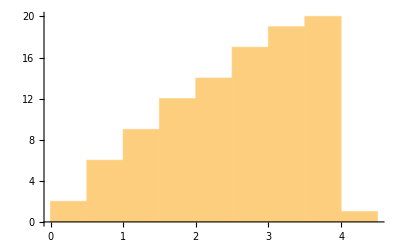

4.

-Graphics-

0.2

-Graphics-

```mathematica
Histogram[zoomLevel,PlotRange->All]
Histogram[geoRange,PlotRange->All]
Max[geoRange]
GeoGraphics[
    Entity["Country","UnitedStates"],
    GeoServer -> "https://api.mapbox.com/v4/mapbox.satellite/``/``/``.png32?access_token=pk.eyJ1IjoicmljY2FyZG9kaXZpcmdpbGlvIiwiYSI6ImNqajhtdHhjNjJkYWozcG9oaHhxa3dzOHQifQ.msWbRUe-nqmNC-DZyl40Ew",
    GeoRange -> Quantity[Max[geoRange],"Miles"]
]
minGeoRange =Min[geoRange]
GeoGraphics[
    Entity["City",{"NewYork","NewYork","UnitedStates"}],
    GeoServer -> "https://api.mapbox.com/v4/mapbox.satellite/``/``/``.png32?access_token=pk.eyJ1IjoicmljY2FyZG9kaXZpcmdpbGlvIiwiYSI6ImNqajhtdHhjNjJkYWozcG9oaHhxa3dzOHQifQ.msWbRUe-nqmNC-DZyl40Ew",
    GeoRange -> Quantity[minGeoRange,"Miles"]
]
```

Create a function to return a association of points and zoom level:

```mathematica
(*associateThePositionsWithGeoRange[points_List] := 
	Map[<|"Point"->#,"Zoom"->getZoomLevel[#]|>&,points];*)
```

Call the createTheDataSet function:

```mathematica
sets = <|
	"training"   -> associateThePositionsWithGeoRange[RandomSample @ trainingDataOfCities],
	"testing"    -> associateThePositionsWithGeoRange[RandomSample @ testingDataOfCities],
	"validation" -> associateThePositionsWithGeoRange[RandomSample @ validationDataOfCities]
|>;
```

RandomSample::lrwl: The set of items to sample from, testingDataOfCities, should be a non-empty list or a rule weights -> choices.

RandomSample::lrwl: The set of items to sample from, validationDataOfCities, should be a non-empty list or a rule weights -> choices.

Let’s now write our function that will encode and decode name of the images:

```mathematica
encodeID[expr_] := StringReplace[Developer`EncodeBase64@BinarySerialize@expr,"/"->"~"]
decodeID[expr_] := BinaryDeserialize@Developer`DecodeBase64ToByteArray@StringReplace[expr,"~"->"/"]
```

Try out the encodeID and decodeID:

```mathematica
Part[assocoatedtrainingData,2]
encodeID[Part[assocoatedtrainingData,2]]
decodeID[%]
```

<|Point→{40.585,-74.1344},Zoom→0.|>

ODpBAi1TBVBvaW50wSMBAly3+ifhSkRA6UeQSZqIUsAtUwRab29tcgAAAAAAAAAA

<|Point→{40.585,-74.1344},Zoom→0.|>

### So, far we have created all the needed functions. Now, we will create our new function that takes all the function and creates folder for a image with association name which was encoded. Then, we will part our image into sub images and store them into the folder we created. This will continue for every image we get using GeoImage.

Create a function to getImages from GeoImage:

```mathematica
ClearAll[getImage]
getImage[coords_List, range_] := 
	GeoGraphics[
        GeoPosition[coords],
        GeoServer -> "https://api.mapbox.com/v4/mapbox.satellite/``/``/``.png32?access_token=pk.eyJ1IjoicmljY2FyZG9kaXZpcmdpbGlvIiwiYSI6ImNqajhtdHhjNjJkYWozcG9oaHhxa3dzOHQifQ.msWbRUe-nqmNC-DZyl40Ew",
        GeoRange -> Quantity[range, "Miles"],
        ImageSize -> {800,800}
    ];
```

Now, let’s create our storeImage function:

```mathematica
ClearAll[imageLocation]

imageLocation[root_, geoRange_, imageNumber_] := 
	FileNameJoin[{root, encodeID[<|"GeoRange" -> geoRange, "Number" -> imageNumber|>] <> ".png"}];
```

Create a function to get folder location with encoded name:

```mathematica
ClearAll[folderLocation]

folderLocation[exp_, trainingOrTestingFolder_] := 
	FileNameJoin[{NotebookDirectory[],trainingOrTestingFolder,encodeID[exp]}];
```

### Okey now it is time to create our function to partition images into smaller parts.

```mathematica
(*When images were parted, their zoom level changed. To prevent that, I also converted the zoom leve for each image by simply dividing the real zoom level with the number of images!*)
ClearAll[partitionTheImage, saveImages]

partitionTheImage[img_,geoRange_ ,levelOfPartition_:3] := 
	Table[
		{geoRange / n, Flatten @ ImagePartition[img, Scaled[1/n]]},
		{n, 1, levelOfPartition}
	];

saveImages[folderName_, partedImage_] := 
	With[
		{zoom = First[partedImage]},
		MapIndexed[
			Export[
				imageLocation[folderName, zoom, Last[#2]], 
				ImageResize[#, {256, 256}]
			] &,
			Flatten @ Last[partedImage]
		]
	]
```

### Time has come, Lets add all the functions:

```mathematica
ClearAll[createTheDataSet]

createTheDataSet[data_List, rest___] := Scan[createTheDataSet[#, rest] &, data]
createTheDataSet[assoPointAndGeoRange_Association, trainingOrTestingFolder_String, rest___] := 
	Module[
		{folderName, img, imglocation},
		folderName = folderLocation[assoPointAndGeoRange, trainingOrTestingFolder];
		If[
			Not @ FileExistsQ @ folderName, 
			Quiet @ CreateDirectory @ folderName;
			img = Image @ getImage[
				assoPointAndGeoRange["Point"], 
				assoPointAndGeoRange["GeoRange"]
			];
			If[
				ImageQ @ img,
				Scan[
					saveImages[folderName, #] &,
					partitionTheImage[img, assoPointAndGeoRange["GeoRange"], rest]
				]
			]
		]
	]
```

```mathematica
(*createTheDataSet[sets["validation"],"validation"]*)
```

```mathematica
(*createTheDataSet[sets["training"],"training"]*)
```

```mathematica
(*createTheDataSet[sets["testing"],"testing"]*)
```

```mathematica
ClearAll[associateThePositionsWithGeoRange]
associateThePositionsWithGeoRange[points_List,zoomLevel_List] := 
	Transpose[<|"Point"->points,"Zoom"->zoomLevel,"GeoRange"->getGeoRange[zoomLevel]|>,AllowedHeads->All]
```

```mathematica
associateThePositionsWithGeoRange[{1,2,3},getZoomLevel[0.2,10,3]]
```

{<|Point→1,Zoom→0.,GeoRange→0.2|>,<|Point→2,Zoom→0.25,GeoRange→2.65|>,<|Point→3,Zoom→1.,GeoRange→10.|>}

```mathematica
ClearAll[createDataSet]
createDataSet[entities_,nPosAndFolder_Association,minRange_,maxRange_] := 
	KeyValueMap[
		Function[
			{name, number},
			createTheDataSet[
				associateThePositionsWithGeoRange[
					 RandomSample [ geoPositionOfCountry[
						{entities},
						number,
						name
					] ],
					RandomSample [ getZoomLevel[
						minRange,
						maxRange,
						number
					] ]
				],
				name
			]
		],
		nPosAndFolder
	]
```

Get training data: DONE!

```mathematica
createDataSet[
{Entity["City",{"Dallas","Texas","UnitedStates"}],Entity["City",{"Chicago","Illinois","UnitedStates"}],Entity["City",{"Houston","Texas","UnitedStates"}]},
<|"training"->290|>,
0.2,
4
]
```

$Aborted

Get validation data:

```mathematica
createDataSet[
{Entity["City",{"Dallas","Texas","UnitedStates"}],Entity["City",{"Chicago","Illinois","UnitedStates"}],Entity["City",{"Houston","Texas","UnitedStates"}]},
<|"validation"->75|>,
0.2,
4
]
```

{Null}

Get testing data :

```mathematica
createDataSet[
{Entity["City",{"Dallas","Texas","UnitedStates"}],Entity["City",{"Chicago","Illinois","UnitedStates"}],Entity["City",{"Houston","Texas","UnitedStates"}]},
<|"testing"->30|>,
0.2,
4
]
```

{Null}

```mathematica
ClearAll[getFileNames,fromFileNameGetGeoRange]
getFileNames[folderName_] := 
	FileNames["*.png",FileNameJoin[{NotebookDirectory[],folderName}],Infinity];
fromFileNameGetGeoRange[fileName_] := 
	decodeID[FileBaseName[fileName]]["GeoRange"];
```

```mathematica
Column @ SortBy[Map[decodeID, FileBaseName/@getFileNames["aho"]], Key["GeoRange"]]
```

```mathematica
fromFileNameGetGeoRange[#]& /@ getFileNames["training"] // Sort//Reverse;
```

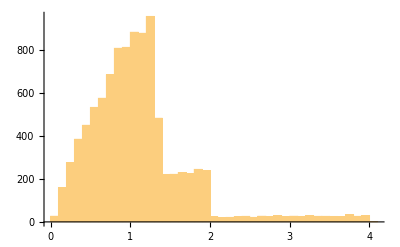

```mathematica
Histogram[fromFileNameGetGeoRange[#]& /@ getFileNames["training"],PlotRange->All ]
```

## Create the Network

In the last section, we collected the satellite images using GeoImage and store all those images on our hard drive. In this section, we will create our Neural Network so we can feed it with the data we have.

Obtain the all the satellite images’ file name:

```mathematica
trainingFileNames = FileNames["*.png","/Users/mehmetsahin/Downloads/SatelliteImages/Training",Infinity];
testingFileNames = FileNames["*.png","/Users/mehmetsahin/Downloads/SatelliteImages/Testing",Infinity];
ByteCount[trainingFileNames]
ByteCount[testingFileNames]
```

3155680

312488

Define a function to get geo range (zoom level) from the image’s name:

```mathematica
fromFileNameGetGeoRange[fileName_] := 
	ToExpression@First@StringSplit[decodeID[FileBaseName@fileName],"-"];
```

Obtain the training and testing data files:

```mathematica
trainingDataFiles = ParallelMap[File[#]->fromFileNameGetGeoRange[#]&,trainingFileNames];
testingDataFiles = ParallelMap[File[#]->fromFileNameGetGeoRange[#]&,testingFileNames];
```

```mathematica
Import[File@First@trainingFileNames]//ImageDimensions
```

{120,133}

```mathematica
Import[File@"/Users/mehmetsahin/Downloads/SatelliteImages/Testing/ODpBAi1TBVBvaW50wSMBAhOrJ8EVmklA5GSwdV05JEAtUwRab29tch+5Dfr4OGE~/ODpTCDYuMjMzNi03.png"]
```

-Graphics-

```mathematica
n[-Graphics-]
```

0.

```mathematica
testingDataFiles // Dataset;
```

Create a dataset of our training data files so it is easier to visualize:

```mathematica
trainingDataFiles//Dataset;
```

```mathematica
netCNNModel = Take[NetModel["Vanilla CNN for Facial Landmark Regression"],{1,"ActivationAbs4"}]
```

NetChain[<>]

```mathematica
NetModel["Vanilla CNN for Facial Landmark Regression"]
```

NetChain[<>]

Define a convolutional neural network that has an "Image" NetEncoder attached to the input port :

```mathematica
lenet=NetChain[{
ConvolutionLayer[16,5,"PaddingSize"->{2,2}],Tanh,Abs,PoolingLayer[2,2],
ConvolutionLayer[48,3,"PaddingSize"->{1,1}],Tanh,Abs,PoolingLayer[2,2],ConvolutionLayer[64,3,"PaddingSize"->{0,0}],Tanh,Abs,PoolingLayer[2,2],ConvolutionLayer[64,2,"PaddingSize"->{0,0}],Tanh,Abs,PoolingLayer[2,2],ConvolutionLayer[128,2,"PaddingSize"->{0,0}],Tanh,Abs,FlattenLayer[],LinearLayer[1000],Tanh,Abs,LinearLayer[100],Tanh,Abs,LinearLayer[10],SoftmaxLayer[],1},"Output"->"Scalar",
"Input"->NetEncoder[{"Image",{120,133}}]
]
```

NetChain[<>]

```mathematica
trainingDataFiles;
```

```mathematica
testFile = trainingDataFiles[[1,1]]
```

File[/Users/mehmetsahin/Downloads/SatelliteImages/Training/ODpBAi1TBVBvaW50wSMBAg1ka+YXMEhAsVsEvF~ZKEAtUwRab29tcvjjAIjV3so~/ODpTCTE4NDcuNTQtMQ==.png]

```mathematica
NetInitialize[lenet][testFile]
```

-0.103362

Train the net for three training rounds :

```mathematica
trained = NetTrain[lenet,trainingDataFiles,All,ValidationSet->testingDataFiles,MaxTrainingRounds->3]
```

NetTrainResultsObject[<>]

```mathematica
trained["TotalTrainingTime"]
```

1230.54

```mathematica
n = trained["TrainedNet"]
```

NetChain[<>]

```mathematica
n[-Graphics-]
```

0.889465

```mathematica
tempnet = Take[NetModel["VGG-16 Trained on ImageNet Competition Data"], {1, "relu3_1"}]
```

NetChain[<>]

## Test the Network

Now ..

## Conclusion

## Author contact information

Mehmet Sahin

6/28/2018
mehmetmshin@gmail.com

## Further Work

Mehmet Sahin

6/28/2018
mehmetmshin@gmail.com